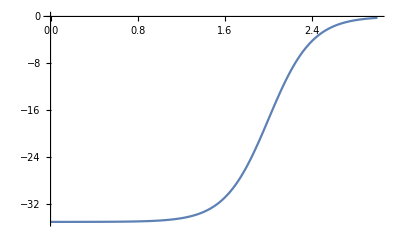

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=35;R=2;a=0.2;μ=8/9 Subscript[m, N];
rmax=3.0;dr=0.01;
rlist=Range[0,rmax,dr];
len=Length[rlist];
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix and eigensystem*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
k[En_]:=Sqrt[(2μ En)/ℏc^2];
B[En_,δ_]:=1+dr Cot[k[En] rmax+δ] k[En];
Hnew[En_,δ_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(-2+B[En,δ]);H)

eigenv[{En_,i_,δ_}]:=({eval,evec}=Eigensystem[Hnew[En,δ]];{eval[[-i]],δ})
```

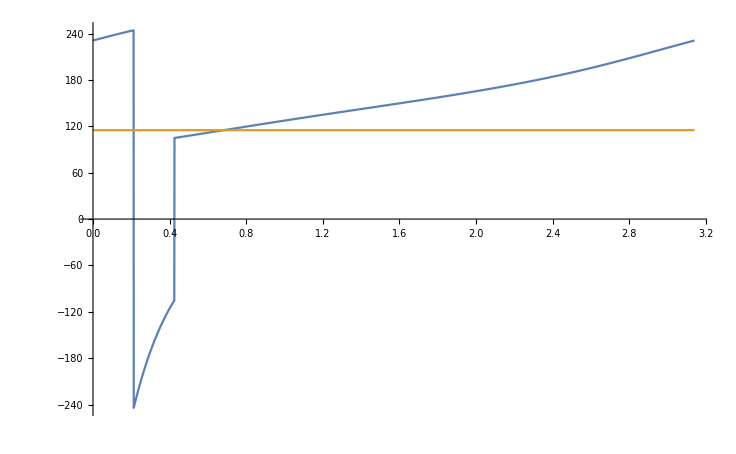

```mathematica
En=115.;
n=3;
(*phase=Table[{eigenv[{En,1,x}][[1]],x},{x,0,Pi,0.01}];*)
(*Solve[eigenv[{En,1,x}]==En,x]*)
(*FindRoot[eigenv[{En,1,δ}][[1]]==En,{δ,0,0,Pi},WorkingPrecision->2]*)
Plot[{eigenv[{En,n,δ}][[1]],#&[En]},{δ,0,Pi},PlotRange->All]
```

```mathematica
phase=Table[{eigenv[{En,n,δ}][[1]],δ},{δ,0.65,0.75,0.001}];
```

```mathematica
δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]]
```

0.683

```mathematica
{eval,evec}=Eigensystem[Hnew[En,δ]];
```

```mathematica
wave[En_,r_,δ_]:=Sin[k[En] r+δ]
const[i_]:=evec[[-i,-1]]/wave[eval[[-i]],rmax,δ]
```

```mathematica
Manipulate[ListLinePlot[{Transpose[{rlist,evec⟦-i⟧}],Transpose[{Range[rmax,rmaxx,dr],const[i] wave[eval[[-i]],Range[rmax,rmaxx,dr],δ]}]},PlotRange->All],{i,1,len,1}]
```

Part::partd: Part specification evec⟦-4⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {rlist,evec⟦-4⟧} cannot be transposed.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Part::partd: Part specification eval⟦-4⟧ is longer than depth of object.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[4] wave[eval⟦-4⟧,Range[rmax,rmaxx,dr],δ]} cannot be transposed.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[4.] wave[eval⟦-4⟧,Range[rmax,rmaxx,dr],δ]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.